# Schwinger Effect in de Sitter Space - Conformal Time Coordinates

## Lagrangian:

## For a free particle in de Sitter space, the Lagrangian (in conformal time coordinates) is:

```mathematica
η'[T]D[-1/(λ^2 η[T]),T] (*Product of first terms of each vector*)
```

η'[T]^2/(λ^2 η[T]^2)

```mathematica
x'[T] D[x[T]/(λ η[T])^2,T](*Product of second terms of each vector*)
```

x'[T] (x'[T]/(λ^2 η[T]^2)-(2 x[T] η'[T])/(λ^2 η[T]^3))

```mathematica
FullSimplify[η'[T]D[-1/(λ^2 η[T]),T]+x'[T] D[x[T]/(λ η[T])^2,T]] (* Product of both vectors *)
```

(-2 x[T] x'[T] η'[T]+η[T] (x'[T]^2+η'[T]^2))/(λ^2 η[T]^3)

```mathematica
LC=FullSimplify[m/(2n)((-η'[T]^2)/(λ η[T])^2+x'[T]^2/(λ η[T])^2)-(m n)/2] (* The Lagrangian *)
```

-(m (n^2 λ^2 η[T]^2-x'[T]^2+η'[T]^2))/(2 n λ^2 η[T]^2)

## Find the equations of motion:

```mathematica
xeqc =FullSimplify[D[D[LC,x'[T]],T]-D[LC,x[T]]==0, Assumptions->{m>0,n>0,λ>0}]
```

x''[T]==(2 x'[T] η'[T])/η[T]

```mathematica
teqc=FullSimplify[D[D[LC,η'[T]],T]-D[LC,η[T]]==0, Assumptions->{m>0,n>0,λ>0}]
```

η''[T]==(x'[T]^2+η'[T]^2)/η[T]

## Solve the equation of motion to get x(T) and η(T):

```mathematica
Clear[solxr,soltr]
```

```mathematica
eta[T_]:=c4/(Cos[c1 T+c2]); 
ex[T_]:=c4 Tan[c2+c1 T]+c3; (* Evaluated by Beatrice *)
```

```mathematica
D[ex[T],T]/(eta[T] λ)
```

(c1 Sec[c2+c1 T])/λ

```mathematica
FullSimplify[Integrate[(c1 Sec[c2+c1 T])/λ,T]]
```

(-Log[Cos[1/2 (c2+c1 T)]-Sin[1/2 (c2+c1 T)]]+Log[Cos[1/2 (c2+c1 T)]+Sin[1/2 (c2+c1 T)]])/λ

```mathematica
(-Log[Cos[1/2 (c2+c1 T)]-Sin[1/2 (c2+c1 T)]]+Log[Cos[1/2 (c2+c1 T)]+Sin[1/2 (c2+c1 T)]])/λ/.T->1
```

(-Log[Cos[(c1+c2)/2]-Sin[(c1+c2)/2]]+Log[Cos[(c1+c2)/2]+Sin[(c1+c2)/2]])/λ

```mathematica
(-Log[Cos[1/2 (c2+c1 T)]-Sin[1/2 (c2+c1 T)]]+Log[Cos[1/2 (c2+c1 T)]+Sin[1/2 (c2+c1 T)]])/λ/.T->0
```

(-Log[Cos[c2/2]-Sin[c2/2]]+Log[Cos[c2/2]+Sin[c2/2]])/λ

```mathematica
FullSimplify[(-Log[Cos[(c1+c2)/2]-Sin[(c1+c2)/2]]+Log[Cos[(c1+c2)/2]+Sin[(c1+c2)/2]])/λ-(-Log[Cos[c2/2]-Sin[c2/2]]+Log[Cos[c2/2]+Sin[c2/2]])/λ]
```

(Log[Cos[c2/2]-Sin[c2/2]]-Log[Cos[c2/2]+Sin[c2/2]]-Log[Cos[(c1+c2)/2]-Sin[(c1+c2)/2]]+Log[Cos[(c1+c2)/2]+Sin[(c1+c2)/2]])/λ

```mathematica
le=Integrate[D[ex[T],T]/(eta[T] λ),{T,0,1}]
```

∫_0^1 (c1 Sec[c2+c1 T])/λ ⅆT

```mathematica
solconst=Solve[{eta[0]==EA,eta[1]==EB,ex[0]==XA,ex[1]==XB},{c1,c2,c3,c4}]/.{C[1]->0,C[2]->0}//Simplify;
```

```mathematica
solini=Simplify[solconst,XB>XA>0&&EA<EB<0]
```

{{c3→(-EA^2+EB^2+XA^2-XB^2)/(2 (XA-XB)),c4→-(√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)))/(2 (XA-XB)),c1→ArcTan[EA^2+EB^2-(XA-XB)^2,√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))],c2→ArcTan[-√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)),EA^2-EB^2+(XA-XB)^2]},{c3→(-EA^2+EB^2+XA^2-XB^2)/(2 (XA-XB)),c4→(√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)))/(2 (XA-XB)),c1→ArcTan[EA^2+EB^2-(XA-XB)^2,-√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))],c2→ArcTan[√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)),EA^2-EB^2+(XA-XB)^2]}}

### Test the solutions by plugging them back into the original equations of motion:

```mathematica
(*Check eom satisfied: should give constants*)
Px=D[ex[T],T]/(H^2 eta[T]^2 ) (*linear momentum in the x-direction along the particle's trajectory*)
En=-(eta[T]D[eta[T],T]-ex[T]D[ex[T],T])/(H^2 eta[T]^2)//Simplify (*(de Sitter) energy along the particle's trajector*)
CQ={Px,En}; (*constants of motion*)
H=1;
dsConstEta= ((Integrate[D[ex[T],T]/(-H eta[T]),T]/.T->1)-(Integrate[D[ex[T],T]/(-H eta[T]),T]/.T->0))//FullSimplify;(*geodesic distance for eta=constant*)
```

c1/c4

(c1 c3)/c4

```mathematica
(*check original eom*)
D[eta[T],{T,2}]-(D[eta[T],T]^2+D[ex[T],T]^2)/eta[T]//Simplify
D[ex[T],{T,2}]-2 D[eta[T],T]D[ex[T],T]/eta[T]
```

0

0

#### Correct solutions!^

## Trajectory plots:

```mathematica
Clear[XA,XB,EA, EB, n,CQ,dsConstEta,solini,par];
```

```mathematica
(*par={XA->1,XB->4,EA-> 1, EB -> 1,λ->-1,n->1(*,m->1*)};
par2={XA->1,XB->4,EA-> 1, EB -> 1,λ->1,n->1(*,m->1,n->1*)};*)(* Different parameters *)
```

```mathematica
par={EA->-5,EB->-5,XA->1,XB->10};
solini/.par//N
{Re[ex[T]/.solini⟦1⟧/.par],Re[eta[T]/.solini⟦1⟧/.par]}/.T->0.5
{Im[ex[T]/.solini⟦1⟧/.par],Im[eta[T]/.solini⟦1⟧/.par]}/.T->0.5
CQ//.solini⟦1⟧//.par//N
dsConstEta//.solini⟦1⟧//.par//N
```

{{c3→5.5,c4→2.17945,c1→2.23954,c2→2.02182},{c3→5.5,c4→-2.17945,c1→-2.23954,c2→1.11977}}

{5.5,-2.17945}

{0,0}

{1.02757,5.65164}

2.94444

```mathematica
sol1=Solve[(solini[[1,2,2]]/.{EA->EB})==0,XB]
```

{{XB→-2 EB+XA},{XB→2 EB+XA}}

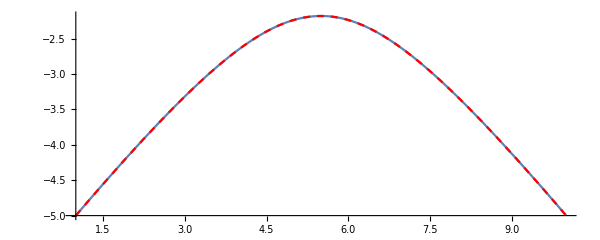

```mathematica
Show[ParametricPlot[{Re[ex[T]/.solini⟦1⟧/.par],Re[eta[T]/.solini⟦1⟧/.par]},{T,0,1}],
ParametricPlot[{Re[ex[T]/.solini⟦2⟧/.par],Re[eta[T]/.solini⟦2⟧/.par]},{T,0,1},PlotStyle->{Red, Dashed}],ImageSize->600]
```

## Simplified expressions for η:

```mathematica
f=soltr[T]/.par
f2=soltr[T]/.par2
```

soltr[T]

ReplaceAll::reps: {par2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

soltr[T]/.par2

## Simplified expressions for x:

```mathematica
g=solxr[T]/.par
g2=solxr[T]/.par2
```

solxr[T]

ReplaceAll::reps: {par2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

solxr[T]/.par2

## Plots of x and η wrt to T :

```mathematica
Plot[{f2,g2},{T,0,1},PlotStyle->{Red,Green}]
```

ReplaceAll::reps: {par2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

## Trajectory for particle in electric field (η versus x) :

```mathematica
ParametricPlot[{g,f},{T,0,1},AspectRatio->1]
```

-Graphics-

## Attempt at Manipulate function:

```mathematica
Clear[xm,tm]
```

```mathematica
(* Variables storing expressions for x and t *)
x
```

x

```mathematica
(*rep={xa->xaa,xb->xbb,ta->taa,tb->tbb,m->mm,n->nn,k->kk};*)
```

```mathematica
eta
```

eta

```mathematica
nnn=n/.Soln[[4]]/.{C[1]->-1} (* General form for the dominant saddle point that we determine later *)
```

Part::partd: Part specification Soln⟦4⟧ is longer than depth of object.

ReplaceAll::reps: {Soln⟦4⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

n/.Soln⟦4⟧

```mathematica
Manipulate[ 
ParametricPlot[{(EB XA Sinh[n (-1+T) λ]-EA XB Sinh[n T λ])/(EB Sinh[n (-1+T) λ]-EA Sinh[n T λ]),(EA EB Sinh[n λ])/(-EB Sinh[n (-1+T) λ]+EA Sinh[n T λ])},{T,0,1},AspectRatio->Full,ImageSize->500,PlotRange->All, AxesLabel->{HoldForm[x[T]],η[T]}]
,
{{XA,0},0,5},
{{XB,5},0,5},
{{EA,1},1,10},
{{EB,1},1,10},
{{λ,1},-5,5},{{n,1},0.1,10}]
```

## Find the classical action:

```mathematica
repl={x[T]->ex[T],η[T]->eta[T],x'[T]->ex'[T],η'[T]->eta'[T]}
```

{x[T]→c3+c4 Tan[c2+c1 T],η[T]→c4 Sec[c2+c1 T],x'[T]→c1 c4 Sec[c2+c1 T]^2,η'[T]→c1 c4 Sec[c2+c1 T] Tan[c2+c1 T]}

```mathematica
L=FullSimplify[LC/.repl] (* Storing the Lagrangian with the solution plugged in *)
```

m (-n/2+c1^2/(2 n λ^2))

```mathematica
S=FullSimplify[Integrate[L,{T,0,1}]] (* Integrating the Lagrangian over T to get the classical action *)
```

m (-n/2+c1^2/(2 n λ^2))

```mathematica
Scl[n_]=FullSimplify[m (-n/2+c1^2/(2 n λ^2))/.solini⟦1⟧]
```

-(m n)/2+(m ArcTan[EA^2+EB^2-(XA-XB)^2,√(-(EA-EB+XA-XB) (EA+EB+XA-XB) (EA-EB-XA+XB) (EA+EB-XA+XB))]^2)/(2 n λ^2)

```mathematica
Scl/.{XA->1,EA->1} (* Using simplified initial values for x and η *)
```

Scl

## Evaluate the prefactor

This is not its derivation but just an evaluation where the prefactor is 1/Sqrt(Det[mx]) where the mx is a matrix with entries given below by Scl1, Scl2, Scl3, and Scl4.

```mathematica
Scl1=D[Scl[n],XA,XB]; (* Evaluating each entry in the matrix *)
```

```mathematica
Scl1-D[Scl[n],XB,XA]//Simplify
```

0

```mathematica
Scl2 = D[Scl[n],XA,EB];
```

```mathematica
Scl2 - D[Scl[n],EB,XA]//Simplify
```

0

```mathematica
Scl3 = D[Scl[n],EA,XB];
```

```mathematica
Scl4 = D[Scl[n],EA,EB];
```

```mathematica
Mx=FullSimplify[({{Scl1, Scl2}, {Scl3, Scl4}})]; (* Plugging in all the evaluated entries *)
```

```mathematica
Pref=FullSimplify[1/(√Det[Mx])] (* Evaluating and simplifying the full prefactor *)
```

1/(√2 √(-(m^2 ArcTan[EA^2+EB^2-(XA-XB)^2,√(-(EA-EB+XA-XB) (EA+EB+XA-XB) (EA-EB-XA+XB) (EA+EB-XA+XB))])/(EA EB n^2 √(-(EA-EB+XA-XB) (EA+EB+XA-XB) (EA-EB-XA+XB) (EA+EB-XA+XB)) λ^4)))

## Figure out how to find the kernel!

#### The kernel is ultimately an integral over N from 0 to ∞ of the integrand below (stored as Int):

```mathematica
Int = FullSimplify[Pref*Exp[ⅈ Scl[n]/ℏ]]
```

(ⅇ^((ⅈ (-(m n)/2+(m ArcTan[EA^2+EB^2-(XA-XB)^2,√(-(EA-EB+XA-XB) (EA+EB+XA-XB) (EA-EB-XA+XB) (EA+EB-XA+XB))]^2)/(2 n λ^2)))/ℏ))/(√2 √(-(m^2 ArcTan[EA^2+EB^2-(XA-XB)^2,√(-(EA-EB+XA-XB) (EA+EB+XA-XB) (EA-EB-XA+XB) (EA+EB-XA+XB))])/(EA EB n^2 √(-(EA-EB+XA-XB) (EA+EB+XA-XB) (EA-EB-XA+XB) (EA+EB-XA+XB)) λ^4)))

However, this integral is extremely difficult (or impossible?) to solve analytically, so we need to use an approximation.

Specifically, we will use a saddle point approximation. That involves allowing N to be complex, and thus allowing the function (i.e. the integrand) to have dependence on complex N (introducing the complex plane). The original contour of the function in the complex plane is very much oscillatory, with an every increasing amplitude of oscillations, which is why it is so tough to solve the integral analytically. Using Cauchy’s theorem, we can deform the original oscillatory contour of the function, which would be a line integral in the 3D-space and restricted to real values of N, to any other “well-behaved” contour such that the contour does not pass over any undefined points (i.e. the function needs to be holomorphic), and the integral over this new contour would be the same as the original contour integral. To quote Wikipedia:  “...if two different paths connect the same two points, and a function is holomorphic everywhere in between the two paths, then the two path integrals of the function will be the same.” (More about holomorphic functions later?) 

Deforming the original path is helpful in the approximation process since the path can be deformed to pass through the highest stationary point/s, with other conditions satisfied of course, and then the path integral would be dominated by that stationary point (or points). It turns out that the only extrema possible in our case are saddle points, so we deform the path to pass through a saddle point (with steepest descent?). [https://www2.ph.ed.ac.uk/~dmarendu/MOMP/lecture05.pdf]

We have been talking about our oscillatory “function” as the whole integrand, but, ignoring the prefactor for now, truly what is relevant is the classical action, Scl, because when we set (d(Int))/dN=0 in order to find the extrema, we get (d(ⅈScl/ℏ))/dN e^(ⅈScl/ℏ)=0 , where the exponent term can’t go to 0, and ⅈ and ℏ are constants, so we know that the extrema are given by (d(Scl))/dN=0, thus the oscillatory function we are concerned with is just Scl.

## Saddle-point approximation

```mathematica
(* Re[fullinteg/.{xa->0,xb->1,ta->0,tb->1,m->1,k->1,ℏ->1}]//FullSimplify *)
```

```mathematica
Plot[Re[Int/.{XA->1,XB->2,EA->-1,EB->-1,m->1,λ-> 1,ℏ->0.1}],{n,2,10},PlotRange->All,AxesLabel->{  HoldForm[N](Lapse), HoldForm[Int]},LabelStyle->{12, GrayLevel[0]}] (* Plot of the function showing oscillatory behavior *)
```

-Graphics-

### Find the saddle points:

```mathematica
Soln = Solve[D[S, n]==0, n] (* Finding the extrema, where C[1] is a constant integer, so there are infinitely many solutions *)
```

{{n→-(ⅈ c1)/λ},{n→(ⅈ c1)/λ}}

```mathematica
FullSimplify[FullSimplify[n/.Soln[[4]]/.C[1]->1] ==FullSimplify[n/.Soln[[3]]/.C[1]->1]]//.{XA->0,XB->2,EA->1,EB->1,m->1,λ-> 1,ℏ->0.1}
```

Part::partw: Part 4 of {{n→-(ⅈ c1)/λ},{n→(ⅈ c1)/λ}} does not exist.

ReplaceAll::reps: {{{n→-(ⅈ c1)/λ},{n→(ⅈ c1)/λ}}⟦4⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {{n→-(ⅈ c1)/λ},{n→(ⅈ c1)/λ}} does not exist.

ReplaceAll::reps: {{{n→-(ⅈ c1)/λ},{n→(ⅈ c1)/λ}}⟦3⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {{n→-ⅈ c1},{n→ⅈ c1}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{{n→-ⅈ c1},{n→ⅈ c1}}⟦3⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

(n/.{{n→-ⅈ c1},{n→ⅈ c1}}⟦3⟧)==(n/.{{n→-ⅈ c1},{n→ⅈ c1}}⟦4⟧)

#### Solve each conditional expression with given parameters and with different choices of C to check for the different saddle points. All the saddle points lie in two vertical lines equidistant from the imaginary axis on both sides (infinite number of saddle points). It turns out later that the saddle point of our concern is one of the four (the fourth one in the given sequence here) acquired by setting C=-1.

```mathematica
Test = {EA->-5,EB->-5,XA->1,XB->12,λ->0.1,m->1};
```

```mathematica
Sp1 = FullSimplify[n/.Soln⟦1⟧/.solini⟦2⟧/.Test]
```

Part::partd: Part specification solini⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {solini⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(0.-10. ⅈ) c1/.solini⟦2⟧

```mathematica
Sp2 = FullSimplify[n/.Soln⟦2⟧/.solini⟦2⟧/.Test]
```

Part::partd: Part specification solini⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {solini⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(0.+10. ⅈ) c1/.solini⟦2⟧

```mathematica
Pl1 = ListPlot[{{Re[Sp1],Im[Sp1]},{Re[Sp2],Im[Sp2]}},PlotStyle->PointSize[Large], PlotRange->All,LabelStyle->{12, GrayLevel[0]}] (* Plot the four saddle points with the given parameters and C=-1 *)
```

-Graphics-

```mathematica
Clear[Sp,Sp1,Sp2,Sp3,Sp4,Test,Test1,Pl1,Pl2]
Clear[Pl2]
```

## Make contour plots of the exponent to put the saddle points in context:

#### Contour plot of the real part of the exponent (Pl2) and the imaginary part of the exponent (Pl3), along with the saddle points (Replot and Implot). As before, we are not yet concerned with the complete function since the exponent suffices in allowing us to make the general approximation:

```mathematica
texStyle={FontSize->14,FontColor->Black};
```

```mathematica
Pl2 = ContourPlot[Re[ⅈ Scl[n]/.Test/.{n->nr+ⅈ ni}],{nr, -50, 50},{ ni, -60, 60}, ColorFunction->"TemperatureMap", Contours->80,LabelStyle->{12, GrayLevel[0]},Frame-> True, AxesLabel->{"Re(N)","Im(N)"},Axes->True,LabelStyle->texStyle,ImageSize->500] (* Contour plot of the real part of the exponent. *)
```

ReplaceAll::reps: {solini⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Test} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {solini⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Replot=Show[Pl2,Pl1] (* Showing with the saddle points *)
```

Show::gcomb: Could not combine the graphics objects in Show[,Pl1].

Show[-Graphics-,Pl1]

```mathematica
Pl3 = ContourPlot[Im[ⅈ Scl[n]/.Test/.{n->nr+ⅈ ni}],{nr, -50, 50},{ ni, -60, 60}, ColorFunction->"TemperatureMap", Contours->80,LabelStyle->{12, GrayLevel[0]},Frame-> True, AxesLabel->{"Re(N)","Im(N)"},Axes->True,LabelStyle->texStyle,ImageSize->500] (* Contour plot of the imaginary part of the exponent. *)
```

ReplaceAll::reps: {solini⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Test} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {solini⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Implot=Show[Pl3,Pl1] (* Showing with the saddle points *)
```

Show::gcomb: Could not combine the graphics objects in Show[,Pl1].

Show[-Graphics-,Pl1]

## Find the lines of steepest descent/ascent:

```mathematica
Sp2
```

Sp2

```mathematica
-(ⅈ π)/3//N
```

0.-1.0472 ⅈ

Make a contour plot of the imaginary part of the exponent for the hopefully-relevant saddle point value of the exponent (Pl4). We are looking for lines of steepest descent/ascent, which have constant imaginary parts, so this allows us to see the lines of steepest descent/ascent that pass through the saddle point/s. Note that n is set to Sp4.

```mathematica
Pl4 = ContourPlot[Im[ⅈ Scl[n]/.Test/.{n->nr+ⅈ ni}]==Im[ⅈ Scl[n]/.Test/.{n->Sp1}],{nr, -60, 60},{ ni, -60, 60}, ColorFunction->"TemperatureMap", Contours->150,LabelStyle->{12, GrayLevel[0]}] (* Contour plot of imaginary part of exponent evaluated at fourth saddle point *)
```

ReplaceAll::reps: {solini⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Test} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {solini⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Lofda=Show[Pl2,Pl1,Pl4] (* Showing altogether the contour for the real part of the exponent (Pl2), the saddle point (Pl1), and the lines of steepest descent/ascent (Pl4) *)
```

Show::gcomb: Could not combine the graphics objects in Show[,Pl1,].

Show[-Graphics-,Pl1,-Graphics-]

```mathematica
(*Pl5 = ContourPlot[Re[ⅈ Scl/.Test/.{n->nr+ⅈ ni}]==Re[ⅈ Scl/ⅇ^0/.Test/.{n->-ⅈ (π+2 ArcCos[√5])}],{nr, -10, 10},{ ni, -10, 10}, ColorFunction->"TemperatureMap", Contours->150]*)
```

## Determine the relevant saddle point/s:

Now, we add a small perturbation to our seemingly endless line of steepest descent/ascent that stems from Sp4 (why?). Explain this step in greater detail. The perturbation is introduced by giving an imaginary component to ℏ (which is set to 1 for now) in the form of ⅇ^ⅈα where α is the perturbation parameter that can be varied to slightly shift the lines of steepest descent/ascent.

```mathematica
Manipulate[
Show[Pl2,Pl1,ContourPlot[Im[ⅈ Scl[n]/.Test/.{n->nr+ⅈ ni}]==Im[ⅈ Scl[n]/ⅇ^(ⅈ α)/.Test/.{n->Sp1}],{nr, -50, 50},{ ni, -50, 50}, ColorFunction->"TemperatureMap", Contours->150,LabelStyle->{12, GrayLevel[0]}]],
{{α,-0.01},-0.1,0.1}
] (* This is the same plot as Lofda except with a small perturbation. *)
```

ReplaceAll::reps: {solini⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Test} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {solini⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,Pl1,].

ReplaceAll::reps: {Test} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,Pl1,].

ReplaceAll::reps: {Test} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,Pl1,].

ReplaceAll::reps: {Test} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,Pl1,].

Lines of steepest descent and ascent have constant imaginary parts - why?

## Evaluate (or rather, approximate) the integral:

Plugging in the expression for  for n for the dominant saddle point (with C[1]=-1) into the expression that we are integrating gives us an approximation to the integral.

```mathematica
Soln
```

{{n→-(ⅈ c1)/λ},{n→(ⅈ c1)/λ}}

```mathematica
Cond={EA->1,EB->1,XA-> XB-l,m->1,λ->1,ℏ->1}; (* Redefining xa and xb in terms of l=xb-xa *)
Cond1={EA->-5,EB->-5,XA->1,λ->10,m->1, ℏ->1};
```

```mathematica
Cond2={EA->-5,EB->-5,XA->1,XB->11,m->1, ℏ->1};
```

```mathematica
FullSimplify[Pref*Exp[ⅈ Scl]/.Cond1 ](* General form of integrand for kernel with given parameters *)
```

ComplexInfinity

```mathematica
g=FullSimplify[Exp[ⅈ S/ℏ]]/.Soln⟦1⟧(* Most general approximation of the integral using saddle point approx. (disregarding prefactor) *)
```

ⅇ^(-(c1 m)/(λ ℏ))

```mathematica
g/.solini⟦2,3⟧/.Cond1
```

Part::partd: Part specification solini⟦2,3⟧ is longer than depth of object.

ReplaceAll::reps: {solini⟦2,3⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ⅇ^(-c1/10)/.solini⟦2,3⟧

```mathematica
Abs[(g/.solini⟦2,3⟧/.Cond1)^2]
```

Part::partd: Part specification solini⟦2,3⟧ is longer than depth of object.

ReplaceAll::reps: {solini⟦2,3⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Abs[ⅇ^(-c1/10)/.solini⟦2,3⟧]^2

For plotting purposes, let' s evaluate g with all parameters defined:

```mathematica
Limit[Abs[(g/.solini⟦2,3⟧/.Cond1)]^2,XB->11]
```

Part::partd: Part specification solini⟦2,3⟧ is longer than depth of object.

ReplaceAll::reps: {solini⟦2,3⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Abs[ⅇ^(-c1/10)/.solini⟦2,3⟧]^2

```mathematica
c1/.solini/.Cond1/.XB->11
```

ReplaceAll::reps: {solini} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

c1/.solini

```mathematica
g
```

ⅇ^(-(c1 m)/(λ ℏ))

```mathematica
(c1/.solini⟦1⟧/.Cond1)/.XB->10//N
```

Part::partd: Part specification solini⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {solini⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

c1/.solini⟦1⟧

```mathematica
Plot[Abs[(g/.solini⟦1⟧/.Cond1)]^2,{XB,1,12},PlotRange->All, AxesLabel->{XB(Distance), P (Probability)},LabelStyle->{12, GrayLevel[0]},ImageSize->600, AspectRatio->1,PlotRange->All]
```

ReplaceAll::reps: {solini⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
solini⟦2,3⟧
```

Part::partd: Part specification solini⟦2,3⟧ is longer than depth of object.

solini⟦2,3⟧

```mathematica
g
```

ⅇ^(-(c1 m)/(λ ℏ))

```mathematica
fxb=Exp[-2c1 m/(λ ℏ)]/.solini[[1]]/.Cond1
```

Part::partd: Part specification solini⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {solini⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ⅇ^(-c1/5)/.solini⟦1⟧

```mathematica
Exp[- 2.23  m/(λ ℏ)]/.Cond1
```

0.800115

```mathematica
fxb/.XB->11
```

ⅇ^(-c1/5)/.solini⟦1⟧

```mathematica
Cond1
```

{EA→-5,EB→-5,XA→1,λ→10,m→1,ℏ→1}

```mathematica
Exp[
```

```mathematica
Cond1
```

{EA→-5,EB→-5,XA→1,λ→10,m→1,ℏ→1}

```mathematica
{EA->-5,EB->-5,XA->1,λ->0g1`,m->1,ℏ->1}
```

```mathematica
(g/.solini⟦1,3⟧)
```

Part::partd: Part specification solini⟦1,3⟧ is longer than depth of object.

ReplaceAll::reps: {solini⟦1,3⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ⅇ^(-(c1 m)/(λ ℏ))/.solini⟦1,3⟧

```mathematica
g
```

ⅇ^(-(c1 m)/(λ ℏ))

```mathematica
Plot[Abs[(g/.solini⟦1⟧/.Cond2)]^2,{λ,0.1,10},PlotRange->All, AxesLabel->{"XB(Distance)", "P (Probability)"},LabelStyle->{12, GrayLevel[0]},ImageSize->600, AspectRatio->1,PlotRange->All] (* Plot of the probability approximation with respect to l (disregarding prefactor) *)
```

ReplaceAll::reps: {solini⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[Abs[(g/.solini⟦1⟧/.Cond1)]^2,{XB,11,12},PlotRange->All, AxesLabel->{"XB(Distance)", "P (Probability)"},LabelStyle->{12, GrayLevel[0]},ImageSize->600, AspectRatio->1,PlotRange->All]
```

ReplaceAll::reps: {solini⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Lcrit=FullSimplify[Reduce[D[(Abs[g])^2, l]==0, {l,λ,m} ]](* Determining the critical distance between the particle and antiparticle (before which they remain virtual particles) *)
```

True

```mathematica
IntApprox = FullSimplify[g/.Lcrit⟦2⟧, m ∈Reals && m>0 && k∈ Reals && k>0]  (* Final approximation of kernel with critical distance and other given parameters *)
```

Part::partd: Part specification True⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {True⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ⅇ^(-(c1 m)/(λ ℏ))/.True⟦2⟧

```mathematica
Prob = IntApprox^2 (* Final approximation of probability with *)
```

(ⅇ^(-(c1 m)/(λ ℏ))/.True⟦2⟧)^2

Use n (saddle point) to plot trajectory.

```mathematica
Fcond={l->2m/k,k->1,m->1};
```

Find derivative of imaginary part of T with respect to internal time, and check which choice of parameters give you negative derivative
ParametricPlot3D for imaginary time, real time, and real x.

```mathematica
Cond2={xa->0,xb->3,ta->0,tb->0,m->1,k->1};
```

```mathematica
ParametricPlot3D[{Re[xm//.n->(2 m (-ⅈ π+ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]))/k//.Cond2],Im[tm//.n->(2 m (-ⅈ π+ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]))/k//.Cond2],Re[tm//.n->(2 m (-ⅈ π+ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]))/k//.Cond2]},{T,0,1},AxesLabel->{Real x, Imaginary t, Real t},LabelStyle->{12, GrayLevel[0]}]
```

-Graphics3D-

#### introduce constant A multiply that with prefactor * everything. Integrate over all possible x and t.

```mathematica
Pref//.Soln⟦1⟧//.solini⟦1⟧//.Cond3//.EB->-1
```

(5 √10)/(√(ArcTan[26-(1-XB)^2,√(-(-5-XB) (-3-XB) (-7+XB) (-5+XB))]/(√(-(-5-XB) (-3-XB) (-7+XB) (-5+XB)) ArcTan[26-(1-XB)^2,√(-625-(1-(1-XB)^2)^2+50 (1+(1-XB)^2))]^2)))

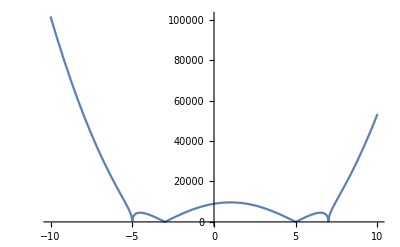

```mathematica
Plot[Abs[Pref//.Soln⟦1⟧//.solini⟦1⟧//.Cond3//.EB->-1]^2,{XB,-10,10}, PlotRange->All]
```

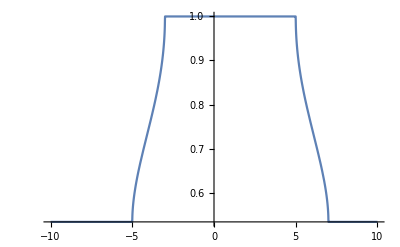

```mathematica
Plot[Abs[Exp[ⅈ Scl[n]/ℏ]//.Soln⟦1⟧//.solini⟦1⟧//.Cond3//.EB->-1]^2,{XB,-10,10}, PlotRange->All]
```

```mathematica
Cond3={EA->-5,XA->1,λ->10,m->1, ℏ->1};
```

```mathematica
FullSimplify[Scl[n],Assumptions->EA<EB<0 && XA<XB && XA∈Reals && XB∈Reals]
```

-(m n)/2+(m ArcTan[EA^2+EB^2-(XA-XB)^2,√(-(EA-EB+XA-XB) (EA+EB+XA-XB) (EA-EB-XA+XB) (EA+EB-XA+XB))]^2)/(2 n λ^2)

```mathematica
Kernel=FullSimplify[Pref*Exp[ⅈ Scl[n]/ℏ]//.Soln⟦1⟧//.solini⟦1⟧]
```

(ⅇ^(-(m ArcTan[EA^2+EB^2-(XA-XB)^2,√(-(EA-EB+XA-XB) (EA+EB+XA-XB) (EA-EB-XA+XB) (EA+EB-XA+XB))])/(λ ℏ)))/(√2 √(m^2/(EA EB √(-(EA-EB+XA-XB) (EA+EB+XA-XB) (EA-EB-XA+XB) (EA+EB-XA+XB)) λ^2 ArcTan[EA^2+EB^2-(XA-XB)^2,√(-(EA-EB+XA-XB) (EA+EB+XA-XB) (EA-EB-XA+XB) (EA+EB-XA+XB))])))

```mathematica
ArcTan[XB,EB]//.XB->1000000//.EB->1000000
```

π/4

```mathematica
ArcTan[25+EB^2-(1-XB)^2,√(-(-4-EB-XB) (-4+EB-XB) (-6-EB+XB) (-6+EB+XB))]/.EB->-1/.XB->10000000
```

Divide::infy: Infinite expression -(1.9999995999995×10^14)/(0``-6.173220025877473) encountered.

ArcTan[-99999979999975,15 ⅈ √44444426666646222226666669]

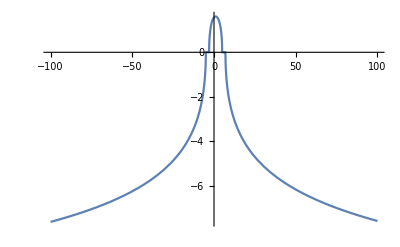

```mathematica
Plot[Im[Evaluate[ArcTan[25+EB^2-(1-XB)^2,√(-(-4-EB-XB) (-4+EB-XB) (-6-EB+XB) (-6+EB+XB))]/.EB->-1]],{XB,-100,100}]
```

```mathematica
nKernel=FullSimplify[Abs[(Kernel//.Cond3)]^2,Assumptions->EA<EB<0 && XA<XB && XA∈Reals && XB∈Reals]
```

-250 ⅇ^(-1/5 Re[ArcTan[EB^2-(-6+XB) (4+XB),√(-(-4+EB-XB) (6+EB-XB) (-6+EB+XB) (4+EB+XB))]]) EB √Abs[(-4+EB-XB) (6+EB-XB) (-6+EB+XB) (4+EB+XB)] Abs[ArcTan[EB^2-(-6+XB) (4+XB),√(-(-4+EB-XB) (6+EB-XB) (-6+EB+XB) (4+EB+XB))]]

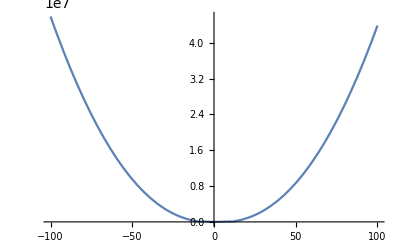

```mathematica
Plot[Evaluate[nKernel/.EB->-5],{XB,-100,100}]
```

```mathematica
(*vars={EB->EA+ΔE,XB->XA+ΔX}*)
```

```mathematica
NIntegrate[Evaluate[-250 ⅇ^(-1/5 Re[ArcTan[EB^2-(-6+XB) (4+XB),√(-(-4+EB-XB) (6+EB-XB) (-6+EB+XB) (4+EB+XB))]]) EB √Abs[(-4+EB-XB) (6+EB-XB) (-6+EB+XB) (4+EB+XB)] Abs[ArcTan[EB^2-(-6+XB) (4+XB),√(-(-4+EB-XB) (6+EB-XB) (-6+EB+XB) (4+EB+XB))]]/.EB->-1],{XB,1,1000000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::inumri: The integrand 250 ⅇ^(-1/5 Re[ArcTan[1-Plus[«2»] Plus[«2»],√(Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»])]]) √Abs[(-5-XB) (5-XB) (-7+XB) (3+XB)] Abs[ArcTan[1-(-6+XB) (4+XB),√((5-XB) (-7+XB) (3+XB) (5+XB))]] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{843751.,851564.}}.

NIntegrate[250 ⅇ^(-1/5 Re[ArcTan[1-(-6+XB) (4+XB),√((5-XB) (-7+XB) (3+XB) (5+XB))]]) √Abs[(-5-XB) (5-XB) (-7+XB) (3+XB)] Abs[ArcTan[1-(-6+XB) (4+XB),√((5-XB) (-7+XB) (3+XB) (5+XB))]],{XB,1,1000000}]

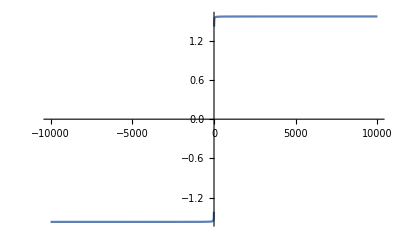

```mathematica
Plot[ArcTan[xx],{xx,-10000,10000}]
```

```mathematica
NIntegrate[ArcTan[25+EB^2-(1-XB)^2,√(-(-4-EB-XB) (-4+EB-XB) (-6-EB+XB) (-6+EB+XB))],{XB,-10000,10000},{EB,-10000,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::inumri: The integrand ArcTan[25+EB^2-(1-XB)^2,√((-4+EB-XB) (-6-EB+XB) (-6+EB+XB) (4+EB+XB))] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{7500.,10000},{0.,-0.028375}}.

NIntegrate[ArcTan[25+EB^2-(1-XB)^2,√(-(-4-EB-XB) (-4+EB-XB) (-6-EB+XB) (-6+EB+XB))],{XB,-10000,10000},{EB,-10000,0}]

```mathematica
Assuming[EA<EB<0 &&XA<XB,Integrate[a (Kernel)^2,XB]]
```

a XB (ComplexInfinity//.solini⟦1⟧)^2

```mathematica
Integrate[a (Kernel)^2,{XB,-∞,∞},{EB,-∞,0}]
```

a ∞ (ComplexInfinity//.solini⟦1⟧)^2

```mathematica
FullSimplify[Solve[Integrate[1/a Kernel^2,{x[T],-∞,∞},{η[T],-∞,∞}]==1,a]]
```

Solve::infc: The system (∞ (ComplexInfinity//.solini⟦1⟧)^2)/a==1 contains an infinite object ∞.

Solve[(∞ (ComplexInfinity//.solini⟦1⟧)^2)/a==1,a]

```mathematica
Δ
```

Δ